## Program TotalAberrations

```mathematica
Off[General::spell1]
Off[General::spell]

TotalAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_]:=
Module[{},
(* number of surfaces and wave lengths *)
n=Length[rad];
m=Length[waves];

(* Distances among the surfaces *)
thicke=Reverse[Take[thick,{1,nstop-1}]];
thicke1=Join[thicke,{0}];
rade=-Reverse[Take[rad,{1,nstop}]]//Flatten;

(* Evaluation of the aperture stop images supplied by the surfaces preceeding the stop:
the last one is the entrance pupil. *)
Do[
inde[h]=Reverse[Take[ind[[h]],{1,nstop}]];
inde1[h]=Prepend[inde[h],1],
{h,1,m}];


Do[
ze[h,1]=If[nstop===0,dis,-dis],
{h,1,3}];

Do[
Do[
Qe[h,i]=(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rade[[i]]-(inde1[h][[i+1]])/w1[h,i]+(inde1[h][[i+1]])/rade[[i]];
ze1[h,i]=Which[ze[h,i]===0,ze[h,i],ze[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,ze[h,i]=!=-Infinity&&Simplify[(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rad[[i]]+(inde1[h][[i+1]])/rad[[i]]]===0,-Infinity,ze[h,i]=!=-Infinity||ze[h,i]===-Infinity,Solve[Qe[h,i]==0,w1[h,i]][[1,1,2]]]; ze[h,i+1]=ze1[h,i]-thicke1[[i]],
{i,1,nstop}],
{h,1,m}];
Do[
de[h]=Which[nstop===0,dis,nstop=!=0,-ze1[h,nstop]],
{h,1,3}];


Do[
ye[h,1]=stoprad;
Do[
ye1[h,i]=If[ze[h,i]=!=0,(inde1[h][[i]] ze1[h,i])/(inde1[h][[i+1]] ze[h,i])ye[h,i],ye[h,i]];
ye[h,i+1]=ye1[h,i],
{i,1,nstop}];
diame[h]=Which[nstop===0,stoprad,nstop=!=0,ye1[h,nstop]],
{h,1,m}];


(* Evaluation of exit pupil *)
thick2=Join[thick,{0}];
Do[
zee[h,1]=de[h];
Do[zee1[h,i]=Which[zee[h,i]===0,0,zee[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,zee[h,i]=!=-Infinity&&Simplify[ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]+ind[[h,i+1]]/rad[[i]]]===0,-Infinity,zee[h,i]=!=-Infinity||zee[h,i]===-Infinity,Solve[Numerator[Together[ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]-ind[[h,i+1]]/fe1[h,i]+ind[[h,i+1]]/rad[[i]]]]==0,fe1[h,i]][[1]][[1,2]]];zee[h,i+1]=zee1[h,i]-thick2[[i]],
{i,1,n}],{h,1,m}];

Do[
yee[h,1]=diame[h];
Do[
yee1[h,i]=Which[zee[h,i]=!=0,(ind[[h,i]] zee1[h,i])/(ind[[h,i+1]] zee[h,i])yee[h,i],zee[h,i]===0,yee[h,i]];
yee[h,i+1]=yee1[h,i],{i,1,n}],
{h,1,m}];

(* Object positions *)
Do[zog[h,1]=dobject,{h,1,m}];
Do[
Do[
zog1[h,i]=Which[zog[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,
zog[h,i]=!=-Infinity&&Simplify[ind[[h,i]]/zog[h,i]-ind[[h,i]]/rad[[i]]+ind[[h,i+1]]/rad[[i]]]===0,-Infinity,zog[h,i]=!=-Infinity||zog[h,i]===-Infinity,
Solve[Numerator[Together[ind[[h,i]]/zog[h,i]-ind[[h,i]]/rad[[i]]-ind[[h,i+1]]/wog1[h,i]+ind[[h,i+1]]/rad[[i]]]]==0,wog1[h,i]][[1]][[1,2]]];
zog[h,i+1]=zog1[h,i]-thick2[[i]],{i,1,n}],
{h,1,m}];


(*Heights of images *)
If[zog[1,1]=!=-Infinity,Goto[a],Goto[b]];

Label[a];
Do[hobj[h,1]=hobject,{h,1,m}];
Do[
Do[hobj1[h,i]=(ind[[h,i]] zog1[h,i])/(ind[[h,i+1]]zog[h,i])hobj[h,i];hobj[h,i+1]=hobj1[h,i],
{i,1,n}],
{h,1,m}];
Goto[c];
Label[b];
Do[
alpha[h,0]=(Pi*angle)/180;
Do[
If[zog[h,i]===-Infinity,alpha[h,i]=-(ind[[h,i]] alpha[h,i-1])/ind[[h,i+1]],Goto[1]];k=i,{i,1,n}],
{h,1,m}];
Label[1];
Do[
hobj1[h,k]=zog1[h,k]*alpha[h,k],
{h,1,m}];
Do[
Do[hobj[h,l]=hobj1[h,l-1];hobj1[h,l]=(ind[[h,l]] zog1[h,l])/(ind[[h,l+1]]zog[h,l])hobj[h,l],
{l,k+1,n}],
{h,1,m}];
Label[c];

(* Object positions of an object at infinity*)
Do[zoginf[h,1]=-Infinity,{h,1,m}];
Do[
Do[
zog1inf[h,i]=Which[zoginf[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,
zoginf[h,i]=!=-Infinity&&Simplify[ind[[h,i]]/zoginf[h,i]-ind[[h,i]]/rad[[i]]+ind[[h,i+1]]/rad[[i]]]===0,-Infinity,zoginf[h,i]=!=-Infinity||zoginf[h,i]===-Infinity,
Solve[Numerator[Together[ind[[h,i]]/zoginf[h,i]-ind[[h,i]]/rad[[i]]-ind[[h,i+1]]/wog1inf[h,i]+ind[[h,i+1]]/rad[[i]]]]==0,wog1inf[h,i]][[1]][[1,2]]];
zoginf[h,i+1]=zog1inf[h,i]-thick2[[i]],{i,1,n}],
{h,1,m}];

(*Heights of images for an object at infinity*)
Do[
alphainf[h,0]=Pi/180 angle,
{h,1,m}];

Do[
Do[
If[zoginf[h,i]===-Infinity,alphainf[h,i]=-(ind[[h,i]] alphainf[h,i-1])/ind[[h,i+1]],Goto[1]];k=i,{i,1,n}];
Label[1];
hobj1inf[h,k]=zog1inf[h,k]*alphainf[h,k],
{h,1,m}];
Do[
Do[hobjinf[h,l]=hobj1inf[h,l-1];hobj1inf[h,l]=(ind[[h,l]] zog1inf[h,l])/(ind[[h,l+1]]zoginf[h,l])hobjinf[h,l],
{l,k+1,n}],
{h,1,m}];
Do[
foc[h]=Which[zog1inf[h,n]===-Infinity,-Infinity,n===1&&Abs[rad[[1]]]=!=Infinity,zog1inf[1,1],n>1,-ind[[h,n+1]]/(ind[[h,1]]alphainf[h,0])hobj1inf[h,n]],
{h,1,m}];

(* Aberrations *)

(* Coefficients of spherical aberrations for stop on the surface*)

Do[
Do[
C1[h,i]=If[Length[costasf[[i]]]==2,-costasf[[i,1]](ind[[h,i+1]]-ind[[h,i]])+(ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2,-costasf[[i]](ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2],
{i,1,n}],
{h,1,m}];

(*Coefficients of coma for stop on the surface*)
Do[
Do[
C2[h,i]=ind[[h,i]]^2/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]]),
{i,1,n}],
{h,1,m}];


(* Coefficients of fields curvature and astigmatism for stop on the surface *)

Do[
Do[
C3[h,i]=ind[[h,i]]/4(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2(1/zog[h,i]-1/rad[[i]]);
C4[h,i]=(-ind[[h,i]]^2)/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))+C3[h,i],
{i,1,n}],
{h,1,m}];

(*Coefficients of distorsion for stop on the surface *)

Do[
Do[
C5[h,i]=-ind[[h,i]]/2(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2,
{i,1,n}],
{h,1,m}];

(* Aberration Coefficients depending on the stop position *)

Do[
Do[
c1[h,i]=If[zog[h,i]===-Infinity,1,zog[h,i]/(zog[h,i]-zee[h,i])];
d1[h,i]=If[zog[h,i]===-Infinity,0,zee[h,i]/(zog[h,i]-zee[h,i])];
k1[h,i]=If[zog[h,i]===-Infinity,zee[h,i],zog[h,i] d1[h,i]];
Cd1[h,i]=c1[h,i]^4 C1[h,i];
Cd2[h,i]=c1[h,i]^2(C2[h,i]-4k1[h,i]C1[h,i]);
Cd3[h,i]=(C3[h,i]-k1[h,i]C2[h,i]+2 k1[h,i]^2 C1[h,i]);
Cd4[h,i]=(C4[h,i]-3k1[h,i]C2[h,i]+6 k1[h,i]^2 C1[h,i]);
Cd5[h,i]=1/c1[h,i]^2(C5[h,i]-2k1[h,i]C4[h,i]+3 k1[h,i]^2 C2[h,i]-4 k1[h,i]^3 C1[h,i]),
{i,1,n}],
{h,1,m}];

(* Magnifications *)

Do[
Do[
Ma[h,i]=hog1[h,i]/hog[h,1];
Mae[h,i]=yee1[h,i]/yee[h,1],
{i,1,n}],
{h,1,m}];

(*Composed system*)
(* Field angle *)
Do[
theta[h]=If[dobject===-Infinity,π/180 angle,hobject/(dobject-zee[h,1])],
{h,1,m}];
(*Total spherical aberration *)
(*If[zog1[1,n]===-Infinity,Goto[g],Goto[f]];
Label[f];*)
Do[
Do[
Absfer[h,i]=If[i==1,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,1] yee[h,1]^3,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,i] Mae[h,i-1]^4 yee[h,1]^3],
{i,1,n}];
Absftot[h]=Sum[Absfer[h,i],{i,1,n}],
{h,1,m}];

(* Total sagittal coma*)
Do[
Comapar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd2[h,1]theta[h] yee[h,1]^2;
Do[
Comapar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] ind[[h,1]]/ind[[h,i]] Mae[h,i-1]^2 Cd2[h,i]theta[h] yee[h,1]^2,
{i,2,n}];
 Comatot[h] =Sum[Comapar[h,i],{i,1,n}],
{h,1,m}];


(* Astigmatism *)
Do[
Astpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](Cd4[h,1]-Cd3[h,1]) theta[h]^2 yee[h,1];
Do[
Astpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]) theta[h]^2 yee[h,1],
{i,2,n}];
Asttot[h] =Sum[Astpar[h,i],{i,1,n}] ,
{h,1,m}];

Do[
Do[
Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),{i,1,n}];
1/Sum[Sp[h,i],{i,1,n}],
{h,1,m}];

Do[
Do[
Curvpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]]^2 ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2 theta[h]^2 yee[h,1],{i,1,n}];
Curvtot[h]=Sum[Curvpar[h,i],{i,1,n}],
{h,1,m}];


(* Distorsion *)
Do[
Distpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd5[h,1] theta[h]^3;
Do[
Distpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2 theta[h]^3 ,
{i,2,n}];
Disttot[h] =Sum[Distpar[h,i],{i,1,n}],
{h,1,m}];


]
```

## Obiettivo Petzval (teoria)

### Esempio OSLO

```mathematica
rad={36.27,-37.87,Infinity,28.42,-22.1,-181.1};
thick={6,2,35.77,6.5,2};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},12.8,2,0.1,-Infinity,y1,7.5,{λ1,λ2,λ3},0]
```

```mathematica
Print["foc. = ",foc[1]]
Print["green back foc. = ",zog1[1,n]]
Print["bleu back foc. = ",zog1[2,n]]
Print["red back foc. = ",zog1[3,n]]
Print["bleu back foc.-red beck foc = ",zog1[2,n]-zog1[3,n]]
Print["ab. sf. = ",Absftot[1]]
Print["coma = ",Comatot[1]]
Print["ast. = ",Asttot[1]]
Print["curv. = ",Curvtot[1]]
```

### L'obiettivo è costituito da due doppiette acromatiche incollate di spessore nullo. Il diaframma è posto tra le due doppiette.

```mathematica
rad={-1200,1/c4,1/c3,-527.473,-527.473,-527.473,1/c3,1/c4};
thick={-415.385,-30,0,0,0,0,30};
ind={{1,-1,-1.5187,-1,-1.5187,1.5187,1,1.5187,1},{1,-1,-1.5224,-1,-1.5224,1.5224,1,1.5224,1},{1,-1,-1.5143,-1,-1.5143,1.5143,1,1.5143,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},100,0,0,-Infinity,y1,0.3,{λ1,λ2,λ3},0]
```

#### Grafici delle funzioni Absftot[1] e Comatot[1] in funzione di c3, c4

```mathematica
ContourPlot[{Absftot[1]==0,Comatot[1]==0},{c3,0.004,0.01},{c4,0.004,0.01}]
```

```mathematica
s2=FindRoot[{Absftot[1]==0,Comatot[1]==0},{c3,0.005},{c4,0.005}]
```

```mathematica
1/s2[[1,2]]
1/s2[[2,2]]
(foc[1])/.s2
(Absftot[1])/.s2
(Comatot[1])/.s2
(zog1[1,n])/.s2
(zog1[2,n])/.s2
(zog1[3,n])/.s2
```

### In tal modo si dispone di 3 raggi (r1, r4, r6) per imporre la focale, il cromatismo assiale e la back focal

```mathematica
rad={1/c1,-1/c1,Infinity,1/c4,-1/c4,1/c6};
thick={0,0,d,0,0};
ind={{1,Subscript[N, 1v],Subscript[N, 2v],1,Subscript[N, 3v],Subscript[N, 4v],1},{1,Subscript[N, 1b],Subscript[N, 2b],1,Subscript[N, 3b],Subscript[N, 4b],1},{1,Subscript[N, 1r],Subscript[N, 2r],1,Subscript[N, 3r],Subscript[N, 4r],1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},R,2,δ,-Infinity,y1,α,{λ1,λ2,λ3}]
```

```mathematica
eqf=Numerator[Together[1/foc[1]-1/f]]//Simplify;
eqcr=Numerator[Together[zog1[2,n]-zog1[3,n]-f/2000]]//Simplify;
eqz=Numerator[Together[zog1[1,n]-d-0.7f]]//Simplify
```

-1.-2. c1 d-1. c4 d+c6 d-1. c1 c4 d^2+c1 c6 d^2-0.7 c1 f-0.7 c4 f+0.7 c6 f-0.7 c1 c4 d f+0.7 c1 c6 d f+2. c4 d N_(3 v)+2. c1 c4 d^2 N_(3 v)+1.4 c4 f N_(3 v)+1.4 c1 c4 d f N_(3 v)-1. c4 d N_(4 v)-1. c6 d N_(4 v)-1. c1 c4 d^2 N_(4 v)-1. c1 c6 d^2 N_(4 v)-0.7 c4 f N_(4 v)-0.7 c6 f N_(4 v)-0.7 c1 c4 d f N_(4 v)-0.7 c1 c6 d f N_(4 v)+c1 N_(2 v) (-2. d-1. c4 d^2+c6 d^2-0.7 f-0.7 c4 d f+0.7 c6 d f+c4 d (2. d+1.4 f) N_(3 v)+d (-1. c4 d-1. c6 d-0.7 c4 f-0.7 c6 f) N_(4 v))+c1 N_v (4. d+2. c4 d^2-2. c6 d^2+1.4 f+1.4 c4 d f-1.4 c6 d f+c4 d (-4. d-2.8 f) N_(3 v)+d (2. c4 d+2. c6 d+1.4 c4 f+1.4 c6 f) N_(4 v))

## Obiettivo Petzval F/1.8-50 (K7-F2-K7-F2) (Oslo)

### Esempio OSLO

```mathematica
rad={36.27,-37.87,Infinity,28.42,-22.1,-181.1};
thick={6,2,35.77,6.5,2};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},12.8,2,0.1,-Infinity,y1,7.5,{λ1,λ2,λ3},0]
```

```mathematica
Print["foc. = ",foc[1]]
Print["green back foc. = ",zog1[1,n]]
Print["bleu back foc. = ",zog1[2,n]]
Print["red back foc. = ",zog1[3,n]]
Print["bleu back foc.-red beck foc = ",zog1[2,n]-zog1[3,n]]
Print["ab. sf. = ",Absftot[1]]
Print["coma = ",Comatot[1]]
Print["ast. = ",Asttot[1]]
Print["curv. = ",Curvtot[1]]
```

### L'obiettivo è costituito da due doppiette acromatiche. Le lenti di entrambe le doppiette sono incollate. Il diaframma è posto tra le due doppiette. Il caso considerato è costituito dai vetri K7-F2-K7-F2, F/1.8, angolo di campo 7.5° e focale 50 mm

```mathematica
rad={-1200,1/c4,1/c3,-527.473,-527.473,-527.473,1/c3,1/c4};
thick={-415.385,-30,0,0,0,0,30};
ind={{1,-1,-1.5187,-1,-1.5187,1.5187,1,1.5187,1},{1,-1,-1.5224,-1,-1.5224,1.5224,1,1.5224,1},{1,-1,-1.5143,-1,-1.5143,1.5143,1,1.5143,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},100,0,0,-Infinity,y1,0.3,{λ1,λ2,λ3},0]
```

#### Grafici delle funzioni Absftot[1] e Comatot[1] in funzione di c3, c4

```mathematica
ContourPlot[{Absftot[1]==0,Comatot[1]==0},{c3,0.004,0.01},{c4,0.004,0.01}]
```

```mathematica
s2=FindRoot[{Absftot[1]==0,Comatot[1]==0},{c3,0.005},{c4,0.005}]
```

```mathematica
1/s2[[1,2]]
1/s2[[2,2]]
(foc[1])/.s2
(Absftot[1])/.s2
(Comatot[1])/.s2
(zog1[1,n])/.s2
(zog1[2,n])/.s2
(zog1[3,n])/.s2
```

### Ipotesi entrambe le doppiette sono incollate, le lenti hanno spessore nullo, r2=-r1, r3=Infinity, r5=-r4, il diaframma è addossato alla prima doppietta In tal modo si dispone di 3 raggi (r1, r4, r6) per imporre la focale, il cromatismo assiale e la back focal

```mathematica
rad={1/c1,-1/c1,Infinity,1/c4,-1/c4,1/c6};
thick={6,2,36,6,2};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},12.8,2,0.1,-Infinity,y1,7.5,{λ1,λ2,λ3}]
```

### Determinazione grafica dei valori di c1 e c4 per c6 fissato.

```mathematica
sa={c6->-1/200.};
ContourPlot[{(foc[1]/.sa)==50,((zog1[2,n]-zog1[3,n])/.sa)==-0.1,(zog1[1,n]/.sa)==20.4,((zog1[2,n]-zog1[1,n])/.sa)==-0.052},{c1,-0.1,0.1},{c4,-0.1,0.1},ContourStyle->{Red,Green,Blue,Yellow}]
```

```mathematica
s0=FindRoot[{foc[1]==50,zog1[2,n]-zog1[3,n]==-0.08, zog1[1,n]==20.4},{c1,0.04},{c4,0.04},{c6,-1/200}]
```

```mathematica
1/s0[[1,2]]
1/s0[[2,2]]
1/s0[[3,2]]
```

### Tutti i raggi sono arbitrari

```mathematica
rad={1/c1,1/c2,Infinity,1/c4,1/c5,1/c6};
thick={6,2,36,6,2};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},12.8,2,0.1,-Infinity,y1,7.5,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==50,zog1[2,n]-zog1[3,n]==-0.08,zog1[1,n]==20.4,Absftot[1]==-0.08,Comatot[1]==-0.009},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c4,s0[[2,2]]},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```

## Obiettivo Petzval F/6-500 (K7-F2-K7-F2)

### L'obiettivo è costituito da due doppiette acromatiche incollate e di spessore nullo. Il diaframma è posto tra le due doppiette. Il caso considerato è costituito dai vetri K7-F2-K7-F2, F/4.5, angolo di campo 4° e focale 150 mm

```mathematica
rad={-1200,1/c4,1/c3,-527.473,-527.473,-527.473,1/c3,1/c4};
thick={-415.385,-30,0,0,0,0,30};
ind={{1,-1,-1.5187,-1,-1.5187,1.5187,1,1.5187,1},{1,-1,-1.5224,-1,-1.5224,1.5224,1,1.5224,1},{1,-1,-1.5143,-1,-1.5143,1.5143,1,1.5143,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},100,0,0,-Infinity,y1,0.3,{λ1,λ2,λ3},0]
```

#### Grafici delle funzioni Absftot[1] e Comatot[1] in funzione di c3, c4

```mathematica
ContourPlot[{Absftot[1]==0,Comatot[1]==0},{c3,0.004,0.01},{c4,0.004,0.01}]
```

```mathematica
s2=FindRoot[{Absftot[1]==0,Comatot[1]==0},{c3,0.005},{c4,0.005}]
```

```mathematica
1/s2[[1,2]]
1/s2[[2,2]]
(foc[1])/.s2
(Absftot[1])/.s2
(Comatot[1])/.s2
(zog1[1,n])/.s2
(zog1[2,n])/.s2
(zog1[3,n])/.s2
```

### In tal modo si dispone di 3 raggi (r1, r4, r6) per imporre la focale, il cromatismo assiale e la lunghezza totale. La distanza tra le doppiette è valutata in modo che la lunghezza totale sia 0.7 foc=105.

```mathematica
rad={1/c1,-1/c1,Infinity,1/c4,-1/c4,1/c6};
thick={0,0,110,0,0};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},20,3,40,-Infinity,y1,4,{λ1,λ2,λ3}]
```

```mathematica
eqf=foc[1]-150;
eqcr=zog1[2,n]-zog1[3,n];
```

### Determinazione grafica dei valori di c1 e c4 per c6 fissato.

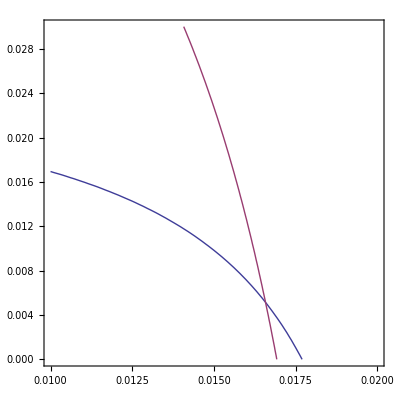

```mathematica
sa={c6->1/300.};
aa=ContourPlot[{(foc[1]/.sa)==150,(zog1[1,n]/.sa)==40},{c1,0.01,0.02},{c4,0,0.03}]
```

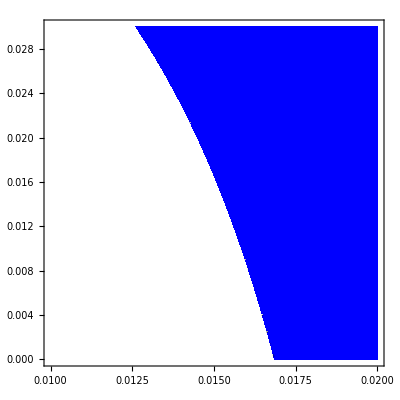

```mathematica
bb=ContourPlot[z=(eqcr/.sa),{c1,0.01,0.02},{c4,0,0.03},RegionFunction->Function[{c1,c4,z},-0.15<z<0.15],Contours->{0.15},ColorFunction->(If[-0.15<#1<0.15,Blue,White]&)]
```

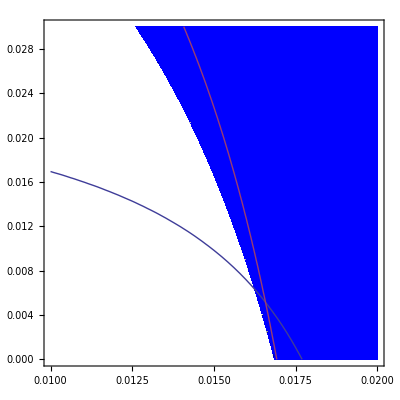

```mathematica
Show[bb,aa]
```

```mathematica
s0=FindRoot[{foc[1]==150,zog1[2,n]-zog1[3,n]==-0.15, zog1[1,n]==40},{c1,0.005},{c4,0.004},{c6,1/300}]
```

{c1→0.0165754,c4→-0.0110233,c6→-0.0071505}

```mathematica
1/s0[[1,2]]
1/s0[[2,2]]
```

60.3303

-90.7169

### Tutti i raggi sono arbitrari

```mathematica
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={10,4,110,4,4};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},13.9,3,3,-Infinity,y1,5,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==150,zog1[2,n]-zog1[3,n]==-0.06,zog1[1,n]==40,Absftot[1]==-0.006,Comatot[1]==0.01,Asttot[1]==-0.001},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c3,-0.00001},{c4,s0[[2,2]]},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

{c1→0.0127824,c2→-0.0118572,c3→-0.000628447,c4→0.0318707,c5→-0.0238966,c6→0.0209277}

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
1/s1[[5,2]]
1/s1[[6,2]]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```

78.2326

-84.3372

-1591.22

31.3768

-41.8469

47.7836

foc. = 150.

green back foc. = 40.

bleu back foc. = 40.0174

red back foc. = 40.0774

ab. sf. = -0.006

coma = 0.01

ast. = -0.001

## Obiettivo Petzval F/6-500 (K7-F2-K7-F2)

### L'obiettivo è costituito da due doppiette acromatiche. Le lenti di entrambe le doppiette sono incollate. Il diaframma è posto tra le due doppiette. Il caso considerato è costituito dai vetri K7-F2-K7-F2, F/6, angolo di campo 2° e focale 500 mm

```mathematica
rad={-1200,1/c4,1/c3,-527.473,-527.473,-527.473,1/c3,1/c4};
thick={-415.385,-30,0,0,0,0,30};
ind={{1,-1,-1.5187,-1,-1.5187,1.5187,1,1.5187,1},{1,-1,-1.5224,-1,-1.5224,1.5224,1,1.5224,1},{1,-1,-1.5143,-1,-1.5143,1.5143,1,1.5143,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},100,0,0,-Infinity,y1,0.3,{λ1,λ2,λ3},0]
```

#### Grafici delle funzioni Absftot[1] e Comatot[1] in funzione di c3, c4

```mathematica
ContourPlot[{Absftot[1]==0,Comatot[1]==0},{c3,0.004,0.01},{c4,0.004,0.01}]
```

```mathematica
s2=FindRoot[{Absftot[1]==0,Comatot[1]==0},{c3,0.005},{c4,0.005}]
```

```mathematica
1/s2[[1,2]]
1/s2[[2,2]]
(foc[1])/.s2
(Absftot[1])/.s2
(Comatot[1])/.s2
(zog1[1,n])/.s2
(zog1[2,n])/.s2
(zog1[3,n])/.s2
```

### Ipotesi entrambe le doppiette sono incollate, le lenti hanno spessore nullo, r2=-r1, r3=Infinity, r5=-r4, il diaframma è posto tra le due doppiette In tal modo si dispone di 3 raggi (r1, r4, r6) per imporre la focale, il cromatismo assiale. La distanza d tra le doppiette è valutata in modo che la lunghezza totale sia d+back focal= 0.7 foc=350. Nella valutazione degli elementi gaussiani non ha importanza la posizione del diaframma.

```mathematica
rad={1/c1,-1/c1,Infinity,1/c4,-1/c4,1/c6};
thick={10,4,280,4,4};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},25.4,3,150,-Infinity,y1,1,{λ1,λ2,λ3}]
```

### Determinazione grafica dei valori di c1 e c4 per c6 fissato.

```mathematica
sa={c6->1/500.};
aa=ContourPlot[{(foc[1]/.sa)==500,(zog1[1,n]/.sa)==50},{c1,0.004,0.01},{c4,-0.024,-0.020},ContourStyle->{Red,Green,Blue,Yellow}]
```

```mathematica
bb=ContourPlot[z=((zog1[2,n]-zog1[3,n])/.sa),{c1,0.004,0.01},{c4,-0.024,-0.020},RegionFunction->Function[{c1,c4,z},-0.1<z<0.1],Contours->{0.1},ColorFunction->(If[-0.1<#1<0.1,Blue,White]&)]
```

```mathematica
Show[aa,bb]
```

```mathematica
Non è possibile progettare questo teleobiettivo
```

```mathematica
ContourPlot[{(foc[1]/.sa)==500,((zog1[2,n]-zog1[3,n])/.sa)==0.05,(zog1[1,n]/.sa)==170,((zog1[2,n]-zog1[1,n])/.sa)==-0.05},{c1,-0.05,0.05},{c4,-0.05,0.05},ContourStyle->{Red,Green,Blue,Yellow}]
```

```mathematica
s0=FindRoot[{foc[1]==500,zog1[2,n]-zog1[3,n]==0.1, zog1[1,n]==170},{c1,0.01},{c4,-0.01},{c6,1/600}]
```

```mathematica
rad={1/s0[[1,2]],-1/s0[[1,2]],1/c3,1/s0[[2,2]],1/c4,1/s0[[3,2]]};
thick={10,4,180,4,4};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},25.4,3,100,-Infinity,y1,1,{λ1,λ2,λ3}]
```

```mathematica
ContourPlot[{foc[1]==500,zog1[2,n]-zog1[3,n]==0.05,zog1[1,n]==170,zog1[2,n]-zog1[1,n]==-0.05},{c3,-0.05,0.05},{c4,-0.05,0.05},ContourStyle->{Red,Green,Blue,Yellow}]
```

```mathematica
rad={1/s0[[1,2]],1/c2,1/c3,1/s0[[2,2]],1/c5,1/c6};
thick={10,4,180,4,4};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},25.4,3,100,-Infinity,y1,1,{λ1,λ2,λ3}]
```

```mathematica
s00=FindRoot[{foc[1]==500,zog1[2,n]-zog1[3,n]==0.1, zog1[1,n]==170,zog1[2,n]-zog1[1,n]==-0.05},{c2,-s0[[1,2]]},{c3,-0.0001},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

### Tutti i raggi sono arbitrari

```mathematica
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={15,4,290,4,4};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},25.5,3,200,-Infinity,y1,1,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==500,zog1[2,n]-zog1[3,n]==0.1,zog1[1,n]==50,Absftot[1]==0.02,Comatot[1]==0.05,Asttot[1]==0.001},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c3,-0.00001},{c4,s0[[2,2]]},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
1/s1[[5,2]]
1/s1[[6,2]]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```

## TeleObiettivo F/5.5-100 (BK7-F2-BK7-F2)(Atmos)

### Esempio Atmos

```mathematica
rad={36.27,-37.87,Infinity,28.42,-22.1,-181.1};
thick={6,2,35.77,6.5,2};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},12.8,2,0.1,-Infinity,y1,7.5,{λ1,λ2,λ3},0]
```

```mathematica
Print["foc. = ",foc[1]]
Print["green back foc. = ",zog1[1,n]]
Print["bleu back foc. = ",zog1[2,n]]
Print["red back foc. = ",zog1[3,n]]
Print["bleu back foc.-red beck foc = ",zog1[2,n]-zog1[3,n]]
Print["ab. sf. = ",Absftot[1]]
Print["coma = ",Comatot[1]]
Print["ast. = ",Asttot[1]]
Print["curv. = ",Curvtot[1]]
```

### L'obiettivo è costituito da due doppiette acromatiche. Le lenti di entrambe le doppiette sono incollate. Il diaframma è posto tra le due doppiette. Il caso considerato è costituito dai vetri BK7-F2-BK7-F2, F/5.5, angolo di campo 5 e focale 100 mm

```mathematica
rad={-1200,1/c4,1/c3,-527.473,-527.473,-527.473,1/c3,1/c4};
thick={-415.385,-30,0,0,0,0,30};
ind={{1,-1,-1.5187,-1,-1.5187,1.5187,1,1.5187,1},{1,-1,-1.5224,-1,-1.5224,1.5224,1,1.5224,1},{1,-1,-1.5143,-1,-1.5143,1.5143,1,1.5143,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},100,0,0,-Infinity,y1,0.3,{λ1,λ2,λ3},0]
```

#### Grafici delle funzioni Absftot[1] e Comatot[1] in funzione di c3, c4

```mathematica
ContourPlot[{Absftot[1]==0,Comatot[1]==0},{c3,0.004,0.01},{c4,0.004,0.01}]
```

```mathematica
s2=FindRoot[{Absftot[1]==0,Comatot[1]==0},{c3,0.005},{c4,0.005}]
```

```mathematica
1/s2[[1,2]]
1/s2[[2,2]]
(foc[1])/.s2
(Absftot[1])/.s2
(Comatot[1])/.s2
(zog1[1,n])/.s2
(zog1[2,n])/.s2
(zog1[3,n])/.s2
```

### Si suppone che le lenti hanno spessore nullo, r2=-r1, r3=Infinity, r5=-r4, r6= Infinity, il diaframma è addossato alla prima doppietta In tal modo si dispone di tre raggi per imporre la focale, il cromatismo di ingrandimento e la back focal

```mathematica
rad={1/c1,-1/c1,Infinity,1/c4,-1/c4,1/c6};
thick={5,2,34,2,5};
ind={{1,1.511121,1.6240808,1,1.511121,1.6240808,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},6.7,3,12,-Infinity,y1,4,{0.54,λ2,λ3}]
```

### Determinazione grafica dei valori di c1 e c4 per c6 fissato.

```mathematica
s0={c6->-1/100};
ContourPlot[{(foc[1]/.s0)==100,((zog1[2,n]-zog1[3,n])/.s0)==0.1,(zog1[1,n]/.s0)==38,((zog1[2,n]-zog1[1,n])/.sa)==-0.05},{c1,-0.1,0.1},{c4,-0.1,0.1},ContourStyle->{Red,Green,Blue,Yellow}]
```

```mathematica
s0=FindRoot[{foc[1]==100,zog1[2,n]-zog1[3,n]==-0.1,zog1[1,n]==38},{c1,0.035},{c4,0.0001},{c6,-1/100}]
```

```mathematica
((zog1[2,n]-zog1[1,n])/.sa)/.s0
```

```mathematica
1/s0[[1,2]]
1/s0[[2,2]]
1/s0[[3,2]]
```

### Si variano 6 raggi per soddisfare tutte le condizioni

```mathematica
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={5,2,34,1.5,4.8};
ind={{1,1.511121,1.6240808,1,1.511121,1.6240808,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},6.7,3,12,-Infinity,y1,4,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==100,zog1[2,n]-zog1[3,n]==-0.1,zog1[1,n]==38,Absftot[1]==-0.032,Comatot[1]==0.0023, Asttot[1]==0.0002},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c3,0.001},{c4,s0[[2,2]]},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
1/s1[[5,2]]
1/s1[[6,2]]
Print["ap. = ", (foc[1]/(2diame[1]))/.s1]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```

```mathematica
diame[1]/.s1
```

```mathematica
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={5,2,34,1.5,4.8};
ind={{1,1.511121,1.6240808,1,1.511121,1.6240808,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},6.7,3,12,-Infinity,y1,4,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==100,zog1[2,n]-zog1[3,n]==-0.1,zog1[1,n]==38,Absftot[1]==-0.032,Comatot[1]==0.0023,Asttot[1]==0.0002},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c3,0.001},{c4,s0[[2,2]]},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
1/s1[[5,2]]
1/s1[[6,2]]
Print["ap. = ", (foc[1]/(2diame[1]))/.s1]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```

```mathematica
rad={1/c1,1/c2,1/c0,1/c3,1/c4,1/c5,1/c6};
thick={5,1,2,34,1.5,4.8};
ind={{1,1.511121,1,1.6240808,1,1.511121,1.6240808,1},{1,1.517002,1,1.632082,1,1.517002,1.632082,1},{1,1.508541,1,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0},6.7,4,12,-Infinity,y1,4,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==100,zog1[2,n]-zog1[3,n]==-0.1,zog1[2,n]-zog1[1,n]==0.01,zog1[1,n]==38,Absftot[1]==-0.032,Comatot[1]==0.0023,Asttot[1]==0.0002},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c0,-s0[[1,2]]},{c3,0.001},{c4,s0[[2,2]]},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
1/s1[[5,2]]
1/s1[[6,2]]
Print["ap. = ", (foc[1]/(2diame[1]))/.s1]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```

## TeleObiettivo F/5.5-100 (BK7-F2-BK7-F2)(Atmos)New

### Esempio Atmos

```mathematica
rad={36.27,-37.87,Infinity,28.42,-22.1,-181.1};
thick={6,2,35.77,6.5,2};
ind={{1,1.511121,1.62004,1,1.511121,1.62004,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},12.8,2,0.1,-Infinity,y1,7.5,{λ1,λ2,λ3},0]
```

```mathematica
Print["foc. = ",foc[1]]
Print["green back foc. = ",zog1[1,n]]
Print["bleu back foc. = ",zog1[2,n]]
Print["red back foc. = ",zog1[3,n]]
Print["bleu back foc.-red beck foc = ",zog1[2,n]-zog1[3,n]]
Print["ab. sf. = ",Absftot[1]]
Print["coma = ",Comatot[1]]
Print["ast. = ",Asttot[1]]
Print["curv. = ",Curvtot[1]]
```

### L'obiettivo è costituito da due doppiette acromatiche. Le lenti della prima doppietta sono incollate. Il diaframma è posto tra le due doppiette. Il caso considerato è costituito dai vetri BK7-F2-BK7-F2, F/5.5, angolo di campo 5 e focale 100 mm

```mathematica
rad={-1200,1/c4,1/c3,-527.473,-527.473,-527.473,1/c3,1/c4};
thick={-415.385,-30,0,0,0,0,30};
ind={{1,-1,-1.5187,-1,-1.5187,1.5187,1,1.5187,1},{1,-1,-1.5224,-1,-1.5224,1.5224,1,1.5224,1},{1,-1,-1.5143,-1,-1.5143,1.5143,1,1.5143,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0,0},100,0,0,-Infinity,y1,0.3,{λ1,λ2,λ3},0]
```

#### Grafici delle funzioni Absftot[1] e Comatot[1] in funzione di c3, c4

```mathematica
ContourPlot[{Absftot[1]==0,Comatot[1]==0},{c3,0.004,0.01},{c4,0.004,0.01}]
```

```mathematica
s2=FindRoot[{Absftot[1]==0,Comatot[1]==0},{c3,0.005},{c4,0.005}]
```

```mathematica
1/s2[[1,2]]
1/s2[[2,2]]
(foc[1])/.s2
(Absftot[1])/.s2
(Comatot[1])/.s2
(zog1[1,n])/.s2
(zog1[2,n])/.s2
(zog1[3,n])/.s2
```

### Ipotesi le lenti hanno spessore nullo, r2=-r1, r3=Infinity, r6=r5, r7=Infinity, il diaframma è posto tra le due doppiette. In tal modo si dispone di tre raggi per imporre la focale, il cromatismo di ingrandimento e la back focal

```mathematica
rad={1/c1,-1/c1,Infinity,1/c4,1/c5,-1/c5,Infinity};
thick={5,2,30,2,2,5};
ind={{1,1.511121,1.6240808,1,1.511121,1,1.6240808,1},{1,1.517002,1.632082,1,1.517002,1,1.632082,1},{1,1.508541,1.615032,1,1.508541,1,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0},5,3,10,-Infinity,y1,5,{0.54,λ2,λ3}]
```

### Determinazione grafica dei valori di c1 e c4 per c5 fissato.

```mathematica
s1={c5->-1/500};
ContourPlot[{(foc[1]/.s1)==100,((zog1[2,n]-zog1[3,n])/.s1)==0.1,(zog1[1,n]/.s1)==38,((zog1[2,n]-zog1[1,n])/.s1)==-0.05},{c1,-0.1,0.1},{c4,-0.1,0.1},ContourStyle->{Red,Green,Blue,Yellow}]
```

```mathematica
s0=FindRoot[{foc[1]==100,zog1[2,n]-zog1[3,n]==-0.1,zog1[1,n]==38},{c1,0.04},{c4,-0.05},{c5,-1/200}]
```

```mathematica
((zog1[2,n]-zog1[1,n]))/.s0
```

```mathematica
1/s0[[1,2]]
1/s0[[2,2]]
1/s0[[3,2]]
```

### Si variano 6 raggi per soddisfare tutte le condizioni

```mathematica
rad={1/c1,1/c2,Infinity,1/c4,1/c5,1/c6,1/c7};
thick={5,2,30,2,2,5};
ind={{1,1.511121,1.6240808,1,1.511121,1,1.6240808,1},{1,1.517002,1.632082,1,1.517002,1,1.632082,1},{1,1.508541,1.615032,1,1.508541,1,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0},5,3,10,-Infinity,y1,5,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==100,zog1[2,n]-zog1[3,n]==-0.1,zog1[1,n]==38,Absftot[1]==-0.032,Comatot[1]==0.0023, Asttot[1]==-0.01},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c4,s0[[2,2]]},{c5,s0[[3,2]]},{c6,-s0[[3,2]]},{c7,-0.001}]
```

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
1/s1[[5,2]]
1/s1[[6,2]]
Print["ap. = ", (foc[1]/(2diame[1]))/.s1]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```

```mathematica
diame[1]/.s1
```

```mathematica
rad={1/c1,1/c2,1/c3,1/c4,1/c5,1/c6};
thick={5,2,34,1.5,4.8};
ind={{1,1.511121,1.6240808,1,1.511121,1.6240808,1},{1,1.517002,1.632082,1,1.517002,1.632082,1},{1,1.508541,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0},6.7,3,12,-Infinity,y1,4,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==100,zog1[2,n]-zog1[3,n]==-0.1,zog1[1,n]==38,Absftot[1]==-0.032,Comatot[1]==0.0023,Asttot[1]==0.0002},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c3,0.001},{c4,s0[[2,2]]},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
1/s1[[5,2]]
1/s1[[6,2]]
Print["ap. = ", (foc[1]/(2diame[1]))/.s1]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```

```mathematica
rad={1/c1,1/c2,1/c0,1/c3,1/c4,1/c5,1/c6};
thick={5,1,2,34,1.5,4.8};
ind={{1,1.511121,1,1.6240808,1,1.511121,1.6240808,1},{1,1.517002,1,1.632082,1,1.517002,1.632082,1},{1,1.508541,1,1.615032,1,1.508541,1.615032,1}};
TotalAberrations[rad,thick,ind,{0,0,0,0,0,0,0},6.7,4,12,-Infinity,y1,4,{λ1,λ2,λ3}]
```

```mathematica
s1=FindRoot[{foc[1]==100,zog1[2,n]-zog1[3,n]==-0.1,zog1[2,n]-zog1[1,n]==0.01,zog1[1,n]==38,Absftot[1]==-0.032,Comatot[1]==0.0023,Asttot[1]==0.0002},{c1,s0[[1,2]]},{c2,-s0[[1,2]]},{c0,-s0[[1,2]]},{c3,0.001},{c4,s0[[2,2]]},{c5,-s0[[2,2]]},{c6,s0[[3,2]]}]
```

```mathematica
1/s1[[1,2]]
1/s1[[2,2]]
1/s1[[3,2]]
1/s1[[4,2]]
1/s1[[5,2]]
1/s1[[6,2]]
Print["ap. = ", (foc[1]/(2diame[1]))/.s1]
Print["foc. = ",foc[1]/.s1]
Print["green back foc. = ",zog1[1,n]/.s1]
Print["bleu back foc. = ",zog1[2,n]/.s1]
Print["red back foc. = ",zog1[3,n]/.s1]
Print["ab. sf. = ",Absftot[1]/.s1]
Print["coma = ",Comatot[1]/.s1]
Print["ast. = ",Asttot[1]/.s1]
```